```mathematica
NetTrain
```

```mathematica
Thread["article"-> {a,b,c,d}]
```

{article→a,article→b,article→c,article→d}

```mathematica
Thread/@{"article"-> {a,b,c,d},"article2"-> {a,b,c,d}}
```

{{article→a,article→b,article→c,article→d},{article2→a,article2→b,article2→c,article2→d}}

```mathematica
Function ->
```

```mathematica
Plot3D[Exp[-α  x],{x,0,10},{α,1,5}]
```

-Graphics3D-

```mathematica
net=NetChain[{LinearLayer[10],Tanh,LinearLayer[1],Tanh},"Input"-> "Real","Output"-> NetDecoder["Scalar"]]
```

NetChain[]

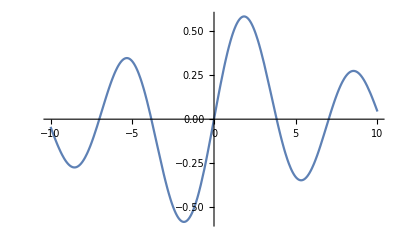

```mathematica
Plot[BesselJ[1,x],{x,-10,10}]
```

```mathematica
trainset=(#-> BesselJ[1,#])&@ RandomReal[{-5,5},100000];
validationset=(#-> BesselJ[1,#])&@RandomReal[{-5,5},10000];
```

```mathematica
trainedNet=NetTrain[net, trainset,ValidationSet->validationset,MaxTrainingRounds->1000]
```

NetChain[]

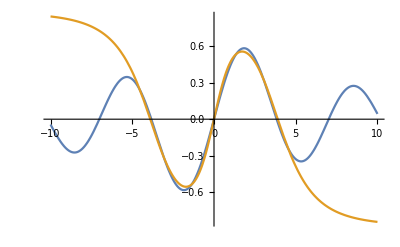

```mathematica
Plot[{BesselJ[1,x],trainedNet[x]},{x,-10,10}]
```

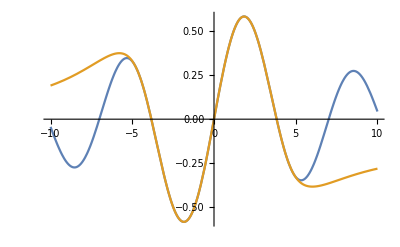

```mathematica
Plot[{BesselJ[1,x],trainedNet[x]},{x,-10,10}]
```

```mathematica
net=NetChain[{LinearLayer[200],Tanh,LinearLayer[1],Tanh},"Input"-> "Real","Output"-> NetDecoder["Scalar"]]
```

NetChain[]

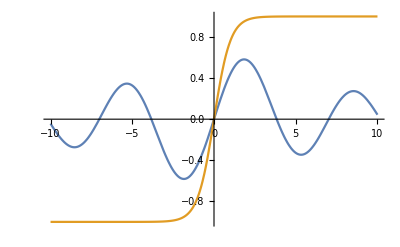

```mathematica
Plot[{BesselJ[1,x],Tanh[x]},{x,-10,10}]
```

```mathematica
trainedNet=NetTrain[net, trainset,ValidationSet->validationset,MaxTrainingRounds->100]
```

NetChain[]

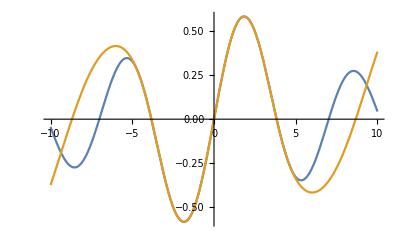

```mathematica
Plot[{BesselJ[1,x],trainedNet[x]},{x,-10,10}]
```

```mathematica
net=NetChain[{LinearLayer[10],Tanh,LinearLayer[10],Tanh,LinearLayer[10],Tanh,LinearLayer[1],Tanh},"Input"-> "Real","Output"-> NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
trainedNet=NetTrain[net, trainset,ValidationSet->validationset,MaxTrainingRounds->100]
```

NetChain[]

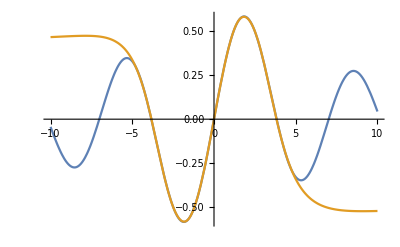

```mathematica
Plot[{BesselJ[1,x],trainedNet[x]},{x,-10,10}]
```